Schwarzschild is working pretty nicely as of DiffGeo5, it still needs to be cleaned up and documented Nicely, but I just really want to try Kerr for now. I’m just going to sub in the new metric, maybe not even play with initial conditions.

```mathematica
(*Initial Conditions*)
L0 = 1.74563;
E0 = 0.910514;
Q0=3.13238;
(*L0 = 3.72737;
E0 = 0.95845;*)
r0 = 7.2;
ϕ0 = 0;
t0=0;
θ0=π/2
M0 = 1;
J0=0.5
NullOrTimelike = -1
```

π/2

0.5

-1

```mathematica
(* Set the dimension and coordinate system *)
d = 4;
coords={t, r, θ, ϕ};
```

```mathematica
(* Define the metric (Kerr time!) *)
rs =2M;
a=J/M;
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-rs r + a^2;
metric={{-1+(rs r)/Σ,0,0,(-rs r a)/Σ},{0,Σ/Δ,0,0},{0,0,Σ,0},{(-rs r a)/Σ,0,0,(r^2+a^2+(rs r a^2)/Σ Sin[θ]^2)Sin[θ]^2}};
metric//MatrixForm
inverseMetric=Simplify[Inverse[metric]];
```

(-1+(2 M r)/(r^2+(J^2 Cos[θ]^2)/M^2) | 0 | 0 | -(2 J r)/(r^2+(J^2 Cos[θ]^2)/M^2)
0 | (r^2+(J^2 Cos[θ]^2)/M^2)/(J^2/M^2-2 M r+r^2) | 0 | 0
0 | 0 | r^2+(J^2 Cos[θ]^2)/M^2 | 0
-(2 J r)/(r^2+(J^2 Cos[θ]^2)/M^2) | 0 | 0 | Sin[θ]^2 (J^2/M^2+r^2+(2 J^2 r Sin[θ]^2)/(M (r^2+(J^2 Cos[θ]^2)/M^2))))

```mathematica
(* Define initial velocities for t and ϕ above, then find initial r-velocity from normalisation of the vector. Set null or timelike path above *)
(*u = {ut, ur, uθ, uϕ};*)
u[α_]:=D[coords[[α]][τ],τ];
metricOfτ=metric/.{t->t[τ],r->r[τ],θ->θ[τ],ϕ->ϕ[τ]};
guuEq = Sum[metricOfτ[[a,b]]u[a]u[b], {a, 1, d}, {b, 1, d}];
(*ur0=Simplify[Solve[guuEq==NullOrTimelike, r'[τ]]][[1]]*)
ur0=Simplify[Solve[guuEq==NullOrTimelike, r'[τ]]][[1]]/.{ r[τ]->r0, t[τ]->t0, θ[τ]->θ0, ϕ[τ]->ϕ0, t'[τ]->-E0/f[r0], θ'[τ]->0, ϕ'[τ]->L0/r0^2, r'[τ]->r'[0]}/.{M->M0, J->J0}
```

{r'[0]→0.-0.0753839 ⅈ}

```mathematica
(* Calculate the Christoffel Symbol *)
Γ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ];
(* Ask Niels if this is a good way to go about it *)
(* Convert the general Christoffel connection to one where the coordinates are functions of time. Really I think this is swapping from the general connection to the connection between different paths or instances of the particle (i.e. we go from r as a coordinate to r_particle(τ) as a component of the position of this object) *)
(* I could also use the metric[τ] I used above but this is cleaner *)
ΓOfτ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ]/.{t->t[τ], r->r[τ], θ->θ[τ], ϕ->ϕ[τ]};
```

```mathematica
(* Get the geodesic equations for each component *)
timeEq=t''[τ]+Sum[ΓOfτ[[1,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
radialEq=r''[τ]+Sum[ΓOfτ[[2,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
θEq=θ''[τ]+Sum[ΓOfτ[[3,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
ϕEq=ϕ''[τ]+Sum[ΓOfτ[[4,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
```

```mathematica
EqsOfM={timeEq==0, radialEq==0, θEq==0, ϕEq==0,r[0]==r0, r'[0]==(r'[0]/.ur0), ϕ[0]==ϕ0, ϕ'[0]==L/r0^2, t[0]==0, t'[0]==-En/f[r0], θ[0]==Pi/2, θ'[0]==0};
```

ReplaceAll::reps: {-0.945588} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
solRange=10;
eomSol = Block[{M=M0, En=E0, L=L0, J=J0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]]
```

{{r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

NDSolve::ndinnt: Initial condition -0.572134 (0.00517196 J+√(0.0000267492 J^2+3.49569 (1.+0.000473739 Power[«2»]+251.64 Plus[«2»]))) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{r,ϕ},{0.000204082,0.,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

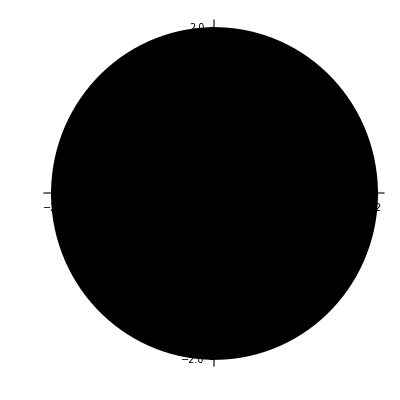

```mathematica
Show[ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}],
Graphics[Disk[{0,0}, 2M0]]]
```